```mathematica
rcap = {Cos[#], Sin[#]} & ;
scap = {Sin[#1] Cos[#2], Sin[#1] Sin[#2], Cos[#1]} & ;
(*rcap[θ]
scap[θ, ϕ]*)
```

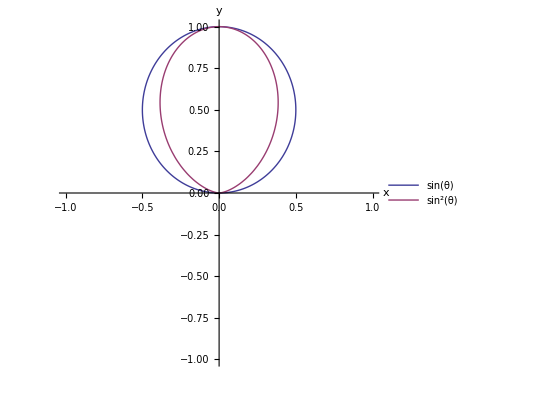

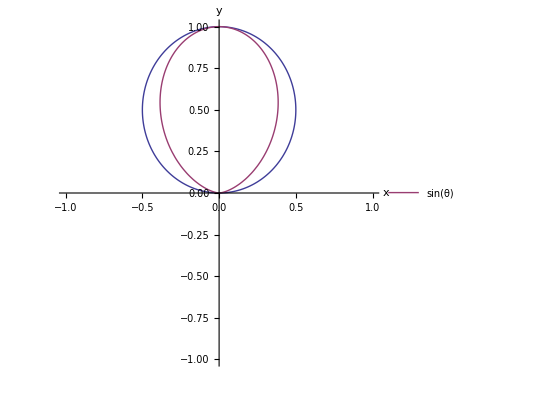

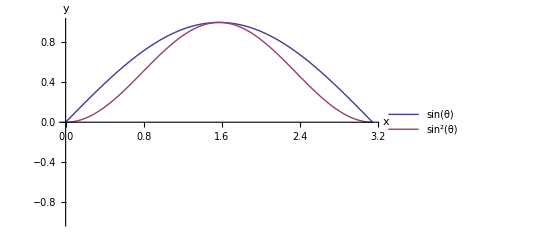

```mathematica
x1 = With[{funcList={Sin[t]rcap[t], Sin[t]^2rcap[t]},
labelList = {"sin(θ)", "sin^2(θ)"}
},With[{n=Length@funcList},Legended[ParametricPlot[funcList,{t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}],LineLegend[(ColorData[1][#])&/@#,labelList[[#]]]&@Range@n]]
]
p1 = ParametricPlot[{Sin[t]rcap[t], Sin[t]^2rcap[t]}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}
,PlotLegends->Placed[{"sin(θ)", "sin^2(θ)"},{Right,Bottom}]
]
(*x1 = Plot[{Sin[t], Sin[t]^2}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}
,PlotLegends->Placed[{"sin(θ)", "sin^2(θ)"},{Right,Bottom}]
]*)
(*s1 = ParametricPlot3D[ {Sin[t]scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]
s2 = ParametricPlot3D[ {Sin[t]^2scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]

p2 = ParametricPlot[{Cos[t]rcap[t], Cos[t]^2rcap[t]}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}]
s3 = ParametricPlot3D[ {Cos[t]scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]
s4 = ParametricPlot3D[ {Cos[t]^2scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}]
*)
```

```mathematica
<<peeters` ;
```

```mathematica
peeters`setGitDir[ "figures/ece1229" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229

```mathematica
peeters`exportForLatex["SineAndSinSq", testplot]
```